# Solving numerically the Lotka-Volterra equations

Defining the parameters of our model

```mathematica
α = 1;
ρ = 1;
β = 0.5;
```

In the following cell we define the numerical solver for the Lotka-Volterra equations.

```mathematica
s=NDSolve[{x'[t]==α*x[t]-ρ*x[t]y[t],y'[t]==-β y[t] + ρ x[t] y[t],x[0]==y[0]==1},{x,y},{t,100}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

Let' s plot as a function of time our numerical solutions:

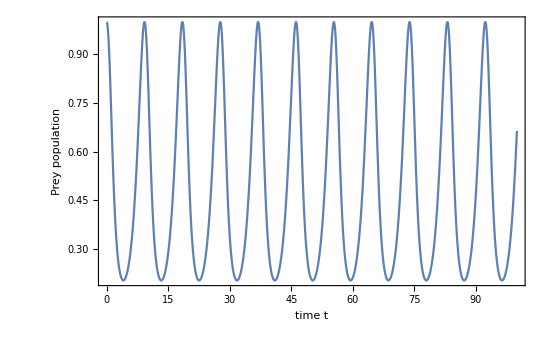

```mathematica
Plot[Evaluate[{x[t]}/.s],{t, 0, 100}, Frame->True,FrameLabel->{"time t","Prey population"},
 LabelStyle->{FontSize->15}]
```

In the following 2 cells we plot a specific solution in the x-y plain and then the entire phase portrait is depicted.

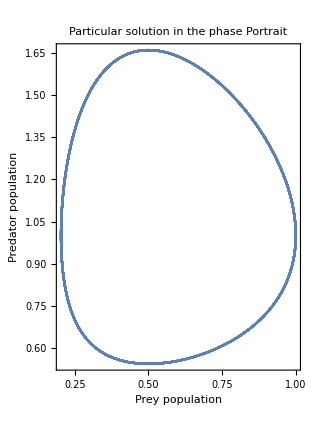

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,100}, Frame->True,FrameLabel->{"Prey population","Predator population"},LabelStyle->{FontSize->15}, PlotLabel-> "Particular solution in the phase Portrait"]
```

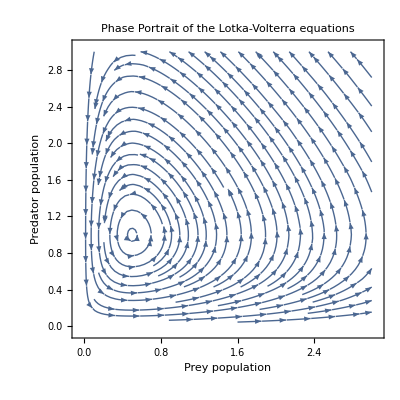

```mathematica
StreamPlot[{α*x[t]-ρ*x[t]y[t], -β y[t] + ρ x[t] y[t]},{x[t],0,3}, {y[t], 0, 3}, PlotLabel-> Style["Phase Portrait of the Lotka-Volterra equations", FontSize->16], Frame->True,FrameLabel->{"Prey population","Predator population"},LabelStyle->{FontSize->15}]
```

```mathematica
f[l_] = Sin[l]
```

```mathematica
f'[l]
```